```mathematica
Clear["Global`*"];
```

```mathematica
xmin=-20;xmax=20; ymin=-10;ymax=10;dx=3;
```

```mathematica
tox=2;
```

```mathematica
V[{x_,y_}]=0.3*Min[((x-xmin)^2-(y-ymin)^2),(x-xmax)^2-(y-ymin)^2]+UnitStep[y-ymax+tox]*3000+UnitStep[-y+ymin+tox]*3000+UnitStep[x-xmax+tox]*3000+UnitStep[-x+xmin+tox]*3000;
```

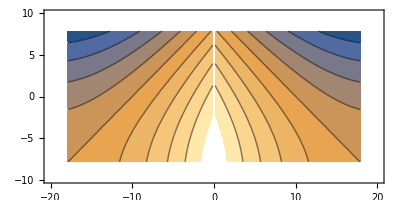

```mathematica
plotV=ContourPlot[V[{x,y}],{x,xmin,xmax},{y,ymin,ymax},AspectRatio->Automatic,PlotRange->{-100,100}]
```

```mathematica
M=200;β=6; τ=β/M;λl=38.9;λT=200.52;
```

```mathematica
A={xmin+tox+1,ymax-tox-1};B={xmax-tox-1,ymax-tox-1};
```

```mathematica
Rio=Join[{A},Table[{RandomReal[{xmin+tox,xmax-tox}],RandomReal[{ymin+tox,ymax-tox}]},{i,2,M}],{B}];
```

```mathematica
(*Rio=Table[{xmin+tox+1+i*L/M,ymax-tox-1},{i,0,M+1}];*)
```

```mathematica
path=ListPlot[Rio];
```

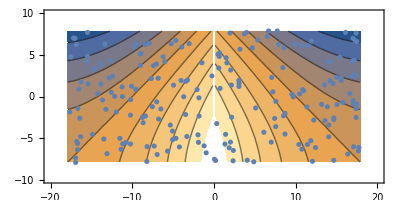

```mathematica
Show[{plotV,path}]
```

```mathematica
Eio=Sum[(Rio[[i,1]]-Rio[[i-1,1]] )^2/(4*λT*τ)+(Rio[[i,2]]-Rio[[i-1,2]] )^2/(4*λl*τ)+τ*V[Rio[[i]]],{i,2,M+1}];
```

```mathematica
dEreg={0};
```

```mathematica
Rireg={Rio};
```

```mathematica
Eireg={Eio};
```

```mathematica
Join[Eireg,{3}];
```

```mathematica
For[icount=1,icount<2000,icount++,
If[Mod[icount,100]==0,Print[icount]];
For[jc=2,jc≤M,jc++,
Ri=Rio;

Ri[[jc]]=Ri[[jc]]+{RandomReal[{-dx,dx}],RandomReal[{-dx,dx}]};

Ei=Eio+
-((Rio[[jc+1,1]]-Rio[[jc,1]] )^2/(4*λT*τ)+(Rio[[jc+1,2]]-Rio[[jc,2]] )^2/(4*λl*τ)+(Rio[[jc,1]]-Rio[[jc-1,1]] )^2/(4*λT*τ)+(Rio[[jc,2]]-Rio[[jc-1,2]] )^2/(4*λl*τ)+τ*V[Rio[[jc]]]) (*remove former contribution*)
+((Ri[[jc+1,1]]-Ri[[jc,1]] )^2/(4*λT*τ)+(Ri[[jc+1,2]]-Ri[[jc,2]] )^2/(4*λl*τ)+(Ri[[jc,1]]-Ri[[jc-1,1]] )^2/(4*λT*τ)+(Ri[[jc,2]]-Ri[[jc-1,2]] )^2/(4*λl*τ)+τ*V[Ri[[jc]]]);(*add new contribution*)
If[RandomReal[]<=Min[1,Exp[-Ei+Eio]],Rio=Ri;Eio=Ei;]];
Eireg=Join[Eireg,{Eio}];Rireg=Join[Rireg,{Rio}];
]
```

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

```mathematica
steps=Dimensions[Rireg][[1]];
```

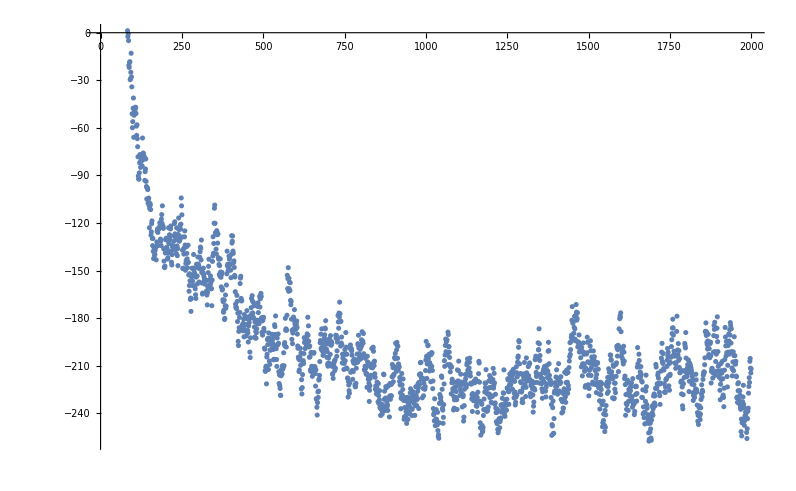

```mathematica
ListPlot[Eireg]
```

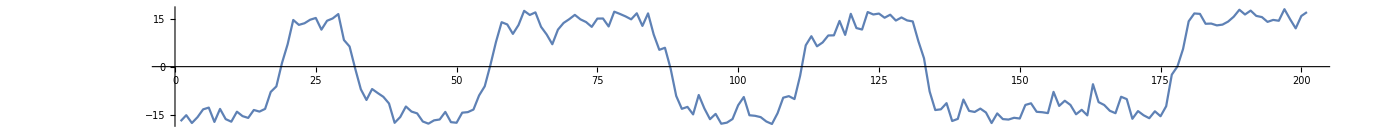

```mathematica
ListPlot[Rireg[[steps,All,1]],Joined->True,AspectRatio->0.1]
```

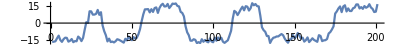

```mathematica
ListPlot[Rireg[[Floor[steps/2],All,1]],Joined->True,AspectRatio->0.1]
```

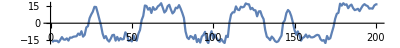

```mathematica
ListPlot[Rireg[[Floor[steps/4],All,1]],Joined->True,AspectRatio->0.1]
```

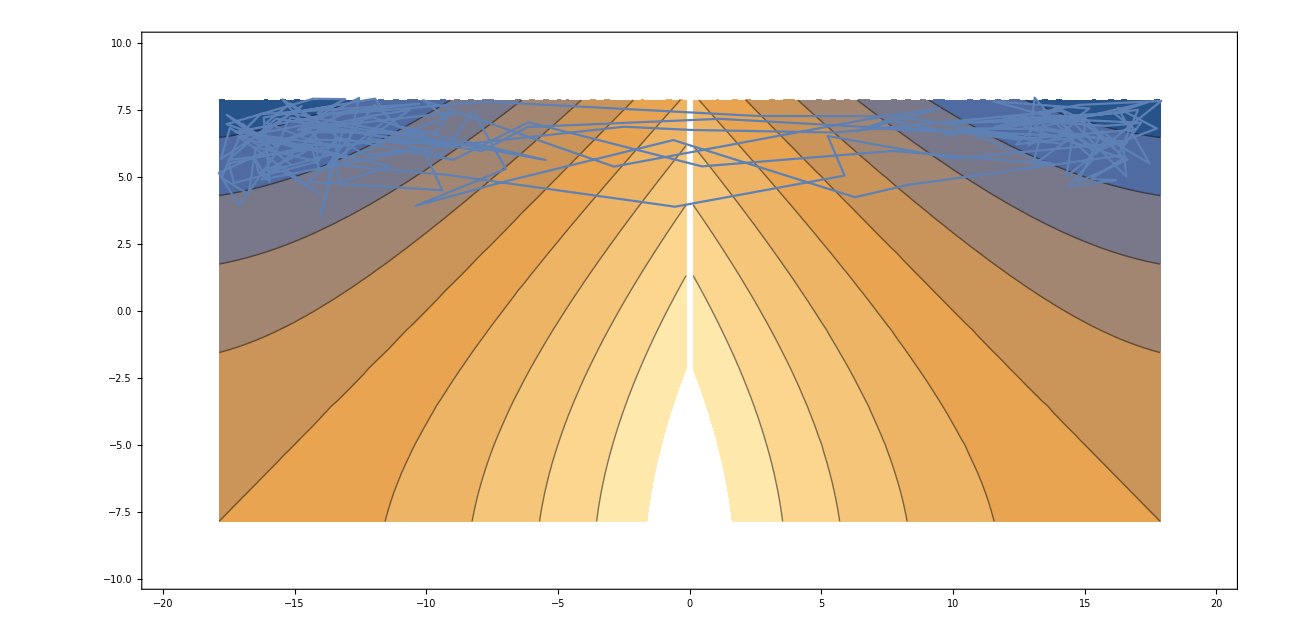

```mathematica
Show[{plotV,ListPlot[Rireg[[steps,All]],Joined->True]}]
```

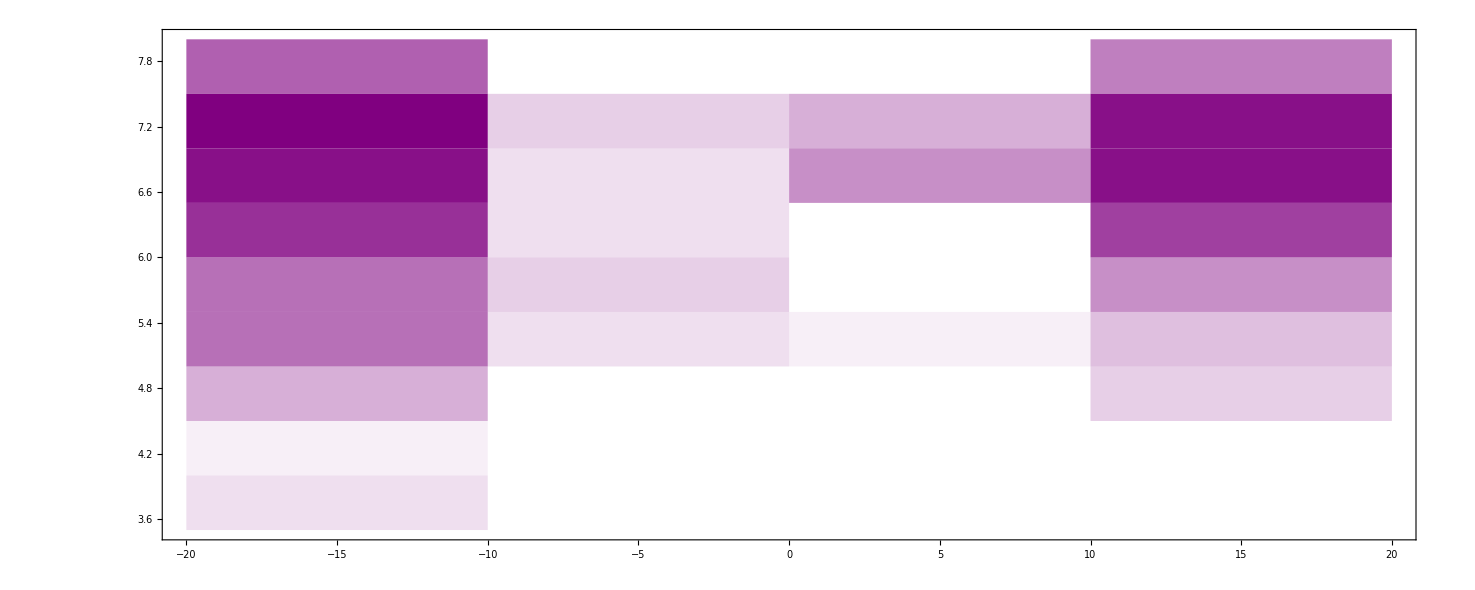

```mathematica
DensityHistogram[Rireg[[steps,All]],AspectRatio->Automatic,ColorFunction->Function[{height},Opacity[height]],ChartBaseStyle->Purple]
```